# DIFFERENCE EQUATIONS

## ELE 489: DIGITAL SIGNAL PROCESSING LABORATORY

Due Date:

## Introduction

In this laboratory you will investigate the software implementation of FIR and IIR systems, namely those defined by non-recursive and recursive difference equations, respectively.

## Problem 1

A non-recursive filter is defined as follows:

y[n]=1/N(x[n]+x[n-1]+...+x[n-N+1])

(a) Obtain the formulas for the impulse and step responses of the given filter.

(b). Implement the system directly from the defining formula using structural programming constructs such as nested Do or For loops only. Verify the correctness of your implementation by computing the impulse and step responses of the system for N=5 and comparing to the closed form solutions obtained in (a).

(c). Apply the filter to the data x obtained in the following evaluation (you are welcome to vary the column value c, note that 1≤c≤109):

```mathematica
c=RandomInteger[{1,109}]
```

15

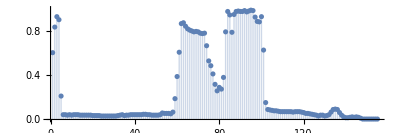

```mathematica
athena=-Graphics-;
x=PixelValue[athena,{c,All}];
ListPlot[x,Filling->0,PlotRange->{0,1},AspectRatio->1/3]
```

Plot the signals x and y. Describe how this system affects the input. Vary the length of the filter N and comment on how the filter length affects the resulting output y?

## Problem 2

A recursive filter is defined:

y[n] =(1-α)x[n] + α y[n-1] , 	0<α<1

(a) Use algebra to obtain the impulse and step responses of the given recursive filter.

(b). Implement the system directly from the defining formula using structural programming constructs such as nested Do or For loops only. Verify the correctness of your implementation by computing the impulse and step responses of the system for a selected value of α and comparing to the closed-form solution obtained in (a).

(c). Apply the filter using α=1/2 and α=3/4 to the data x obtained in the following evaluation (you are welcome to vary the column value c, note that 1≤c≤109):

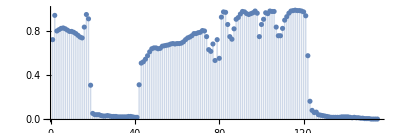

```mathematica
c=30;
athena=-Graphics-;
x=PixelValue[athena,{c,All}];
ListPlot[x,Filling->0,PlotRange->{0,1},AspectRatio->1/3]
```

Plot the signals x and y. Describe how this system affects the input. How does the output change as the value of parameter α is varied?

## Problem 3

A recursive filter is defined:

y[n] - α y[n-D] = x[n],

(a) Use algebra to obtain the impulse and step responses of the recursive filter for α=2/3 and D=2.

(b). Implement the system directly from the defining formula using structural programming constructs such as nested Do or For loops only. Verify the correctness of your implementation by computing the impulse and step responses of the system for α=2/3 and D=2 and comparing to the closed-form solution obtained in (a).

(c). Apply the filter using α=2/3 and D=2000 to the signal x created here:

```mathematica
audio=AudioResample[ExampleData[{"Audio","PianoScale"}],8000];
x=AudioData[audio]⟦1⟧;
```

Play the signals x and y using function Audio as shown here:

```mathematica
Audio[x,SampleRate->8000]
```

Describe how this system affects the input? How does the output change as the values of the parameters 0<α<1 and 100<D<4000 are varied?